```mathematica
Manipulate[
Module[{coil},
coil=Graphics[
Inset[
Show[
ParametricPlot3D[{u,Sin[5*u],Cos[5*u]},{u,0,10},PlotStyle->Red,ViewPoint->Front]/.Line[pts_,rest___]:>Tube[pts,0.2,rest],
ParametricPlot3D[{v,0.4*Sin[-5*v],0.5*Cos[-5*v]},{v,-6.5,10},PlotStyle->Blue,ViewPoint->Front]/.Line[pts_,rest___]:>Tube[pts,0.2,rest],
PlotRange->All,(*{{-3,10},{-1.15,1.15},{-1.15,1.15}},*)Boxed->False,ImageSize->500,(*ImageSize->{360,72},*)Axes->False],{1.75,0}]];
Show[
(*coil,*)
Graphics[{
{Thickness[0.007],Line[{{-2.5,-1.15},{-0.25,-0.75},{0,-0.75},{0,-1.25},{2,-1.25},{2,-1},{10,-1},{10,1},{2,1},{2,1.25},{1.75,1.25},{1.75,2.5},{0,2.5},{0,1.25},{-0.25,1.25},{-0.25,0.75},{-2.5,1.15},{-2.5,-1.15}}]},
{EdgeForm[{Thickness[0.007],Black}],White,Polygon[{{ϕ-1.75,0},{ϕ,0.8},{ϕ,-0.8}}]},
{Thickness[0.007],Arrowheads[0.03],Arrow[{{-1.5,3.75},{0.875,3.75},{0.875,2.55}}],Arrow[{{-2.55,0},{-4.05,0}}],Arrow[{{ϕ,0},{ϕ+1.5,0}}]},
Text[Style[Column[{"T_f = 25 °C","(m^·)_f = 88 g/min"}],15],{-3.25,3.75}],
Text[Style[Column[{"T_C = 20 °C","(m^·)_C = 60 g/min"}],15],{-5.75,0}],
Text[Style[Column[{"T_H = 36 °C","(m^·)_H = 28 g/min"}],15],{ϕ+4,0}]
}],PlotRange->{{-8,17.25},{-1.5,5}},ImageSize->600]
],
Control[{{ϕ,10.25,""},10.25,11,0.01,Appearance->"Labeled"}]]
```

```mathematica
(*Graphics[
Inset[*)
Show[
ParametricPlot3D[{u,Sin[5*u],Cos[5*u]},{u,0,10},PlotStyle->Red,ViewPoint->Front]/.Line[pts_,rest___]:>Tube[pts,0.2,rest],
ParametricPlot3D[{v,0.4*Sin[-5*v],0.5*Cos[-5*v]},{v,-6.5,10},PlotStyle->Blue,ViewPoint->Front]/.Line[pts_,rest___]:>Tube[pts,0.2,rest],
PlotRange->{{-6.5,10},{-1.15,1.15},{-1.15,1.15}},Boxed->False,ImageSize->400,(*ImageSize->{360,72},*)Axes->False](*,{1.75,0}]]*)
```

-Graphics3D-

```mathematica
ImageDimensions[-Graphics3D-]
```

{400,56}

```mathematica
1.75/2
```

0.875

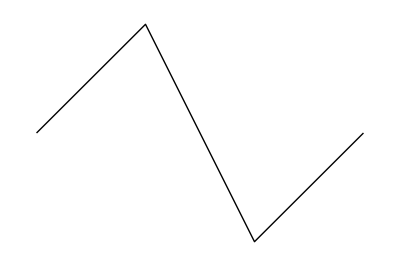

```mathematica
Graphics[Line[{{0,0},{1,1},{2,-1},{3,0}}]]
```

```mathematica
Graphics[
Line[Ta
]
```

```mathematica
-2.55-2.5
```

-5.05

```mathematica
10.25-8.5
```

1.75

```mathematica
4.05-2.55
```

1.5